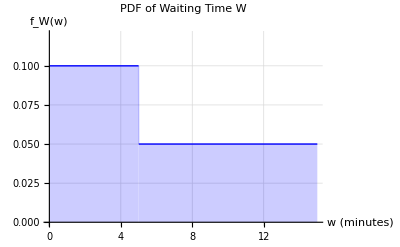

```mathematica
(*Define the piecewise pdf of W*)fW[w_]:=Piecewise[{{1/10,0≤w<5},{1/20,5≤w≤15},{0,True}}];

(*Plot the density function*)
Plot[fW[w],{w,0,15},AxesLabel->{"w (minutes)","f_W(w)"},PlotStyle->{Thick,Blue},Filling->Axis,PlotRange->{{0,15},{0,0.12}},GridLines->Automatic,PlotLabel->"PDF of Waiting Time W"]
```